```mathematica
g=9.8;
l=0.5;
c = 3 10^8;
m = 1;
vt = Sqrt[m g/c];
ode1=x''[t]==(-g x'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2];
ode2 = y''[t] == -g(1+ (y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]);
sol=NDSolve[{{ode1,x[0]==0,x'[0]==50},{ode2, y[0]==0, y'[0]==30}},{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

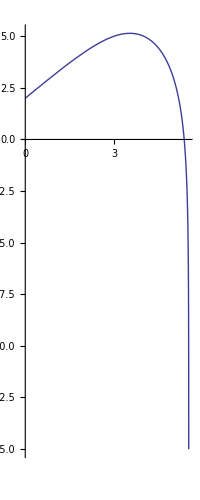

-Graphics-

```mathematica
v = 30;
θ = 50*π/180;
sol=NDSolve[{ode1,x[0]==0,x'[0]==v Cos[θ],ode2, y[0]==2, y'[0]==v Sin[θ]},{x,y},{t,0,200}];
myplot1=ParametricPlot[{x[t] /.sol[[1]][[1]], y[t] /. sol[[1]][[2]]},{t,0,5},PlotRange-> All]
Show[myplot1]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,0,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,10,"v_0 (m/s)"},10,200,Appearance->"Labeled"},
{{vt,10,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"θ_0 (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

# CannonBall

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,1,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,10,"v_0 (m/s)"},10,200,Appearance->"Labeled"},
{{vt,135,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"θ_0 (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

# Human Cannonball

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,10,"v_0 (m/s)"},10,200,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"θ_0 (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

# Golfball

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,0,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,10,"v_0 (m/s)"},10,200,Appearance->"Labeled"},
{{vt,44,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"θ_0 (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

# Baseball

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],
{{y0,1.5,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,10,"v_0 (m/s)"},10,200,Appearance->"Labeled"},
{{vt,43,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.1,"θ_0 (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
data = {{ ,CWCannon,HmnCannon,Baseball,Golfball},{Angle Speed},{Angle  Speed},{Angle Speed}}
Grid[data,Alignment->Left]
```

```mathematica
{{Null,CWCannon,HmnCannon,Baseball,Golfball},{Angle Speed,0.4794 36},{Angle Speed,0.582421 34},{Angle Speed,0.6118,34}}
```

{{Null,CWCannon,HmnCannon,Baseball,Golfball},{Angle Speed,17.2584},{Angle Speed,19.8023},{Angle Speed,0.6118,34}}

## tables are hard

# (B)

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,8000},{-10,500}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,439,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.0872664626,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,8000},{-10,500}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,439,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.174532925,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,8000},{-10,800}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,439,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.261799388,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

# (C)

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,1000},{-10,500}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,238,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.0872664626,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,1000},{-10,500}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,170,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.174532925,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol =NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t] == -g(1+ (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),
{x[0]==0, y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th]t,y0 + v Sin[th]t-0.5g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,1000},{-10,800}},ImageSize->{500,300}]],
{{y0,2,"y_0 (m)"},0,200,Appearance->"Labeled"},
{{v,140,"v_0 (m/s)"},10,500,Appearance->"Labeled"},
{{vt,60,"v_terminal (m/s)"},10,200,Appearance->"Labeled"},
{{th,0.261799388,"θ_0 (rad)"},0,π/2,Appearance->"Labeled"},
{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```